```mathematica
α = π/4;
g = 9.8;
tMax = 1.564132866713876;
```

```mathematica
solutions = NDSolveValue[
{
r''[t]==(r[t] ϕ'[t]^2- g Cot[α])/Csc[α]^2,
ϕ''[t]== -(2 ϕ'[t])/r[t],
r[0] ==1,r'[0]==0,
ϕ[0]==0,ϕ'[0]==5
},
{r[t],ϕ[t]},
{t,0,tMax}
]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

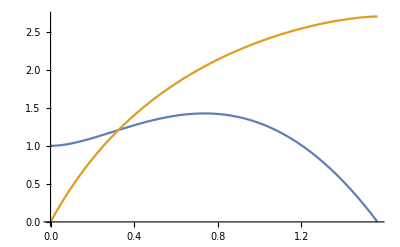

```mathematica
Plot[solutions,{t,0,tMax},PlotRange->All]
```

```mathematica
rV[r_,ϕ_]:={r Cos[ϕ],r Sin[ϕ], r Cot[α]};
rV[tp_]:=Apply[rV,solutions/.t->tp];
```

```mathematica
Show[
Graphics3D[{Opacity[0.4],Cone[{{0,0,2},{0,0,0}},2]}],
ParametricPlot3D[rV[t],{t,0,tMax}]
]
```

-Graphics3D-

```mathematica
Manipulate[
Show[
Graphics3D[
{
Opacity[0.4],
Cone[{{0,0,2},{0,0,0}},2],
Opacity[1],
Sphere[rV[t],0.1]
}
],
ParametricPlot3D[rV[tp],{tp,0,t}]
],
{t,0.0001,tMax}
]
```